```mathematica
u[x_,y_]:=Cos[y]/(x^2+y^2)
```

```mathematica
Plot3D[u[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Solve[y-2 ArcTan[ⅇ^(-2 ArcTanh[Tan[x/2]]+k)]==0,k]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→2 ArcTanh[Tan[x/2]]+Log[Tan[y/2]]}}

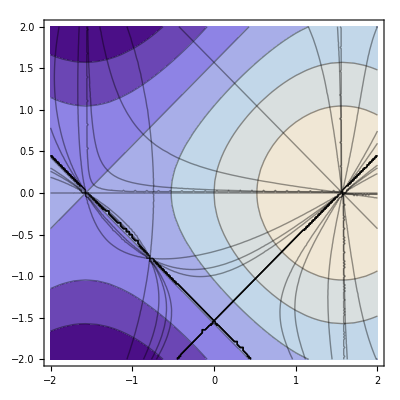

```mathematica
Show[
ContourPlot[u[x,y],{x,-2,2},{y,-2,2}],
ContourPlot[2 ArcTanh[Tan[x/2]]+Log[Tan[y/2]],{x,-2,2},{y,-2,2},ContourShading->None],
ContourPlot[(y Cos[x]+x Sin[y])/(Cos[x]+Sin[y]),{x,-2,2},{y,-2,2},ContourShading->None]
]
```

```mathematica
D[u[x,y],y]/D[u[x,y],x]
```

```mathematica
-((x^2+y^2)^2 Sec[y] (-(2 y Cos[y])/((x^2+y^2)^2)-Sin[y]/(x^2+y^2)))/(2 x)/.y->y[x]
```

-(Sec[y[x]] (x^2+y[x]^2)^2 (-(2 Cos[y[x]] y[x])/((x^2+y[x]^2)^2)-Sin[y[x]]/(x^2+y[x]^2)))/(2 x)

```mathematica
DSolve[y'[x]==-(Sec[y[x]] (x^2+y[x]^2)^2 (-(2 Cos[y[x]] y[x])/((x^2+y[x]^2)^2)-Sin[y[x]]/(x^2+y[x]^2)))/(2 x),y[x],x]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

DSolve[y'[x]==-(Sec[y[x]] (x^2+y[x]^2)^2 (-(2 Cos[y[x]] y[x])/((x^2+y[x]^2)^2)-Sin[y[x]]/(x^2+y[x]^2)))/(2 x),y[x],x]